# Top Neynar Scores with Low Reach

```mathematica
neynar = Import["/home/jalil/Programs/farcaster-deno/data/neynar_scores.csv", "Tabular"];
quotient = Import["/home/jalil/Programs/farcaster-deno/data/fids_reputation_20250508.csv", "Tabular"];
merged =  JoinAcross[neynar,quotient,"fid"];
```

```mathematica
cutpoint = 1000;
combinedCutTop1000 = merged// 
ReverseSortBy["neynar_score"] // (#[[1;;cutpoint, {"fid","username", "cred_score", "bridge_score", "neynar_score"}]])& // 
SortBy["cred_score"];
combinedCutBottom1000 = JoinAcross[neynar,quotient,"fid"] // 
ReverseSortBy["neynar_score"] // (#[[cutpoint;;, {"fid","username", "cred_score", "bridge_score", "neynar_score"}]])& // 
SortBy["cred_score"];
```

```mathematica
r1 = combinedCutTop1000[[All, "neynar_score"]] // Normal; r2 = combinedCutTop1000[[All, "cred_score"]] // Normal;
r3 = combinedCutBottom1000[[All, "neynar_score"]] // Normal; r4 = combinedCutBottom1000[[All, "cred_score"]] // Normal;
rankedTop1000 = Transpose[{r1,r2}];
rankedBottom1000= Transpose[{r3,r4}];

Histogram3D[{ rankedTop1000, rankedBottom1000},ChartLabels->Placed[{"Top 1000","Bottom 1000"},Above,"Framed"],
ChartLayout -> "Stacked",
PlotLabel->"Heatmap of Rank Pairs"]
```

-Graphics3D-

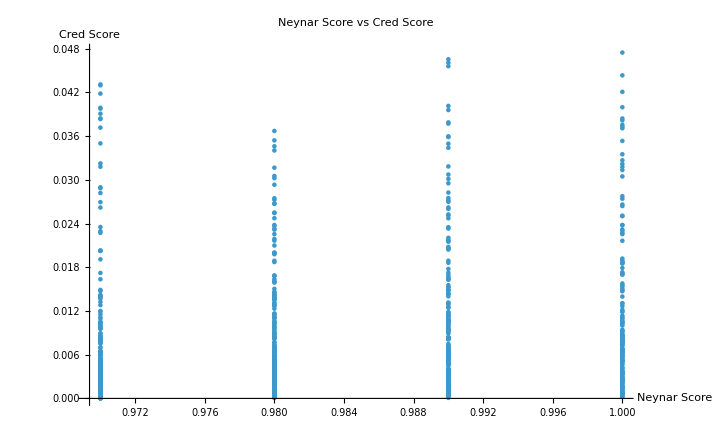

```mathematica
p1 =ListPlot[rankedTop1000,
PlotLabel -> "Neynar Score vs Cred Score",
AxesLabel-> {"Neynar Score", "Cred Score"},
ColorFunction-> (ColorData[{"SunsetColors","Reverse"}][(#2 * 5) + 0.4]&)
]
```

```mathematica
Export["/home/jalil/Programs/farcaster-deno/data/Top_Neynar_vs_Cred.jpg",p1,"JPEG"]
```

/home/jalil/Programs/farcaster-deno/data/Top_Neynar_vs_Cred.jpg

```mathematica
combinedCutTop1000 // ReverseSortBy[{"neynar_score", "cred_score"}]
```